```mathematica
Binomial[7,2]
```

21

```mathematica
7*6
```

42

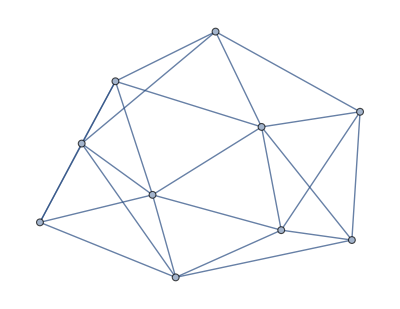

```mathematica
With[{n=10},RandomGraph[{n,3n-6}]]
```

```mathematica
Ff=FindFullFormula[%]
```

```mathematica
Map[SetsToPartitionTypeSymbol[SymbolToSets[#]]&,Ff]//Total
```

p1x1x1x1x1x1x1x1x1x1+21 p2x1x1x1x1x1x1x1x1+140 p2x2x1x1x1x1x1x1+343 p2x2x2x1x1x1x1+264 p2x2x2x2x1x1+29 p2x2x2x2x2+4 p3x1x1x1x1x1x1x1+41 p3x2x1x1x1x1x1+104 p3x2x2x1x1x1+58 p3x2x2x2x1+3 p3x3x1x1x1x1+9 p3x3x2x1x1+3 p3x3x2x2

```mathematica
PartitionTypeFormula[g_]:=Total[Map[With[{p=SetsToPartitionTypeSymbol[SymbolToSets[#]]},
If[SymbolLevel[p]<=4,Style[p,Darker[Green],Bold],p]]&,FindFullFormula[g]]]
```

```mathematica
DoItFroGraph[g_]:=Block[{edges=Sort[EdgeList[GraphComplement[g]]]},
Monitor[
Table[e<->Framed[Column[{PartitionTypeFormula[VertexContract[g,{e[[1]],e[[2]]}]],PartitionTypeFormula[EdgeAdd[g,e]]}]],
{e,edges}
],
e]
]
```

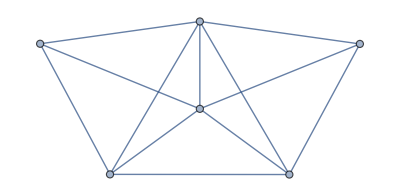

```mathematica
g=With[{n=6},RandomGraph[{n,3n-6}]]
```

```mathematica
DoItFroGraph[g]//TableForm
```

1<->6<->p1x1x1x1x1+p2x1x1x1
p1x1x1x1x1x1+2 p2x1x1x1x1
2<->5<->p1x1x1x1x1+p2x1x1x1
p1x1x1x1x1x1+2 p2x1x1x1x1
5<->6<->p1x1x1x1x1
p1x1x1x1x1x1+2 p2x1x1x1x1+p2x2x1x1

```mathematica
MaximalPlanarQ[g]
```

True

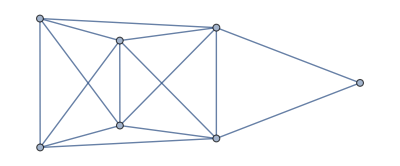
-Graphics-p1x1x1x1x1x1x1+6 p2x1x1x1x1x1+7 p2x2x1x1x1+2 p2x2x2x1

1<->2<->p1x1x1x1x1x1+4 p2x1x1x1x1+2 p2x2x1x1
p1x1x1x1x1x1x1+5 p2x1x1x1x1x1+3 p2x2x1x1x1
1<->6<->p1x1x1x1x1x1+p2x1x1x1x1
p1x1x1x1x1x1x1+5 p2x1x1x1x1x1+6 p2x2x1x1x1+2 p2x2x2x1
3<->4<->p1x1x1x1x1x1+4 p2x1x1x1x1+2 p2x2x1x1
p1x1x1x1x1x1x1+5 p2x1x1x1x1x1+3 p2x2x1x1x1
3<->6<->p1x1x1x1x1x1+p2x1x1x1x1
p1x1x1x1x1x1x1+5 p2x1x1x1x1x1+6 p2x2x1x1x1+2 p2x2x2x1
5<->6<->p1x1x1x1x1x1+2 p2x1x1x1x1+p2x2x1x1
p1x1x1x1x1x1x1+5 p2x1x1x1x1x1+5 p2x2x1x1x1+p2x2x2x1
6<->7<->p1x1x1x1x1x1+2 p2x1x1x1x1+p2x2x1x1
p1x1x1x1x1x1x1+5 p2x1x1x1x1x1+5 p2x2x1x1x1+p2x2x2x1

```mathematica
With[{g=With[{n=7},RandomGraph[{n,3n-6}]]},
Print[Labeled[g,PartitionTypeFormula[g]]];
DoItFroGraph[g]//TableForm
]
```

```mathematica
Table[PartitionTypeFormula[ReadGrof[k]],{k,10}]//TableForm
```

p1x1x1x1
p1x1x1x1x1+p2x1x1x1
p1x1x1x1x1x1+3 p2x1x1x1x1+p2x2x1x1
p1x1x1x1x1x1+3 p2x1x1x1x1+3 p2x2x1x1+p2x2x2
p1x1x1x1x1x1x1+6 p2x1x1x1x1x1+7 p2x2x1x1x1+p2x2x2x1
p1x1x1x1x1x1x1+6 p2x1x1x1x1x1+9 p2x2x1x1x1+4 p2x2x2x1
p1x1x1x1x1x1x1+6 p2x1x1x1x1x1+10 p2x2x1x1x1+5 p2x2x2x1
p1x1x1x1x1x1x1+6 p2x1x1x1x1x1+6 p2x2x1x1x1+p3x1x1x1x1+p3x2x1x1
p1x1x1x1x1x1x1+6 p2x1x1x1x1x1+6 p2x2x1x1x1+p3x1x1x1x1+p2x2x2x1
p1x1x1x1x1x1x1x1+10 p2x1x1x1x1x1x1+25 p2x2x1x1x1x1+15 p2x2x2x1x1+p2x2x2x2

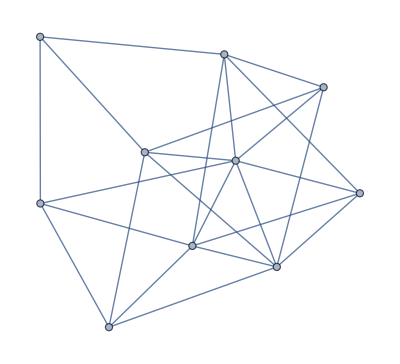
-Graphics-p1x1x1x1x1x1x1x1x1x1+21 p2x1x1x1x1x1x1x1x1+136 p2x2x1x1x1x1x1x1+308 p2x2x2x1x1x1x1+202 p2x2x2x2x1x1+16 p2x2x2x2x2+10 p3x1x1x1x1x1x1x1+96 p3x2x1x1x1x1x1+207 p3x2x2x1x1x1+87 p3x2x2x2x1+16 p3x3x1x1x1x1+34 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+8 p3x3x2x2+p4x3x2x1

1<->2<->p1x1x1x1x1x1x1x1x1+14 p2x1x1x1x1x1x1x1+55 p2x2x1x1x1x1x1+67 p2x2x2x1x1x1+19 p2x2x2x2x1+5 p3x1x1x1x1x1x1+26 p3x2x1x1x1x1+26 p3x2x2x1x1+2 p3x3x1x1x1+4 p3x2x2x2+p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+125 p2x2x1x1x1x1x1x1+280 p2x2x2x1x1x1x1+187 p2x2x2x2x1x1+16 p2x2x2x2x2+7 p3x1x1x1x1x1x1x1+65 p3x2x1x1x1x1x1+144 p3x2x2x1x1x1+64 p3x2x2x2x1+7 p3x3x1x1x1x1+17 p3x3x2x1x1+4 p3x3x2x2
1<->4<->p1x1x1x1x1x1x1x1x1+13 p2x1x1x1x1x1x1x1+48 p2x2x1x1x1x1x1+52 p2x2x2x1x1x1+12 p2x2x2x2x1+3 p3x1x1x1x1x1x1+17 p3x2x1x1x1x1+15 p3x2x2x1x1+2 p3x3x1x1x1+p3x2x2x2+p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+125 p2x2x1x1x1x1x1x1+276 p2x2x2x1x1x1x1+177 p2x2x2x2x1x1+13 p2x2x2x2x2+8 p3x1x1x1x1x1x1x1+78 p3x2x1x1x1x1x1+173 p3x2x2x1x1x1+74 p3x2x2x2x1+12 p3x3x1x1x1x1+28 p3x3x2x1x1+7 p3x3x2x2
1<->6<->p1x1x1x1x1x1x1x1x1+14 p2x1x1x1x1x1x1x1+56 p2x2x1x1x1x1x1+68 p2x2x2x1x1x1+18 p2x2x2x2x1+4 p3x1x1x1x1x1x1+23 p3x2x1x1x1x1+23 p3x2x2x1x1+2 p3x3x1x1x1+3 p3x2x2x2+p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+125 p2x2x1x1x1x1x1x1+278 p2x2x2x1x1x1x1+182 p2x2x2x2x1x1+15 p2x2x2x2x2+7 p3x1x1x1x1x1x1x1+67 p3x2x1x1x1x1x1+150 p3x2x2x1x1x1+66 p3x2x2x2x1+8 p3x3x1x1x1x1+20 p3x3x2x1x1+5 p3x3x2x2
1<->8<->p1x1x1x1x1x1x1x1x1+14 p2x1x1x1x1x1x1x1+53 p2x2x1x1x1x1x1+56 p2x2x2x1x1x1+13 p2x2x2x2x1+5 p3x1x1x1x1x1x1+25 p3x2x1x1x1x1+18 p3x2x2x1x1+2 p3x3x1x1x1+2 p3x2x2x2
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+123 p2x2x1x1x1x1x1x1+265 p2x2x2x1x1x1x1+169 p2x2x2x2x1x1+13 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+81 p3x2x1x1x1x1x1+162 p3x2x2x1x1x1+67 p3x2x2x2x1+13 p3x3x1x1x1x1+24 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+6 p3x3x2x2+p4x3x2x1
1<->9<->p1x1x1x1x1x1x1x1x1+13 p2x1x1x1x1x1x1x1+44 p2x2x1x1x1x1x1+37 p2x2x2x1x1x1+3 p2x2x2x2x1+4 p3x1x1x1x1x1x1+17 p3x2x1x1x1x1+9 p3x2x2x1x1+p3x3x1x1x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+123 p2x2x1x1x1x1x1x1+264 p2x2x2x1x1x1x1+165 p2x2x2x2x1x1+13 p2x2x2x2x2+10 p3x1x1x1x1x1x1x1+92 p3x2x1x1x1x1x1+190 p3x2x2x1x1x1+78 p3x2x2x2x1+16 p3x3x1x1x1x1+33 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+8 p3x3x2x2+p4x3x2x1
1<->10<->p1x1x1x1x1x1x1x1x1+15 p2x1x1x1x1x1x1x1+63 p2x2x1x1x1x1x1+79 p2x2x2x1x1x1+21 p2x2x2x2x1+5 p3x1x1x1x1x1x1+28 p3x2x1x1x1x1+28 p3x2x2x1x1+2 p3x3x1x1x1+4 p3x2x2x2+p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+122 p2x2x1x1x1x1x1x1+256 p2x2x2x1x1x1x1+151 p2x2x2x2x1x1+10 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+80 p3x2x1x1x1x1x1+155 p3x2x2x1x1x1+55 p3x2x2x2x1+12 p3x3x1x1x1x1+21 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+3 p3x3x2x2+p4x3x2x1
2<->3<->p1x1x1x1x1x1x1x1x1+13 p2x1x1x1x1x1x1x1+43 p2x2x1x1x1x1x1+33 p2x2x2x1x1x1+2 p2x2x2x2x1+4 p3x1x1x1x1x1x1+16 p3x2x1x1x1x1+6 p3x2x2x1x1+p3x3x1x1x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+123 p2x2x1x1x1x1x1x1+265 p2x2x2x1x1x1x1+169 p2x2x2x2x1x1+14 p2x2x2x2x2+10 p3x1x1x1x1x1x1x1+92 p3x2x1x1x1x1x1+191 p3x2x2x1x1x1+81 p3x2x2x2x1+16 p3x3x1x1x1x1+33 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+8 p3x3x2x2+p4x3x2x1
2<->4<->p1x1x1x1x1x1x1x1x1+14 p2x1x1x1x1x1x1x1+56 p2x2x1x1x1x1x1+64 p2x2x2x1x1x1+14 p2x2x2x2x1+4 p3x1x1x1x1x1x1+25 p3x2x1x1x1x1+21 p3x2x2x1x1+4 p3x3x1x1x1+p3x2x2x2+p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+124 p2x2x1x1x1x1x1x1+269 p2x2x2x1x1x1x1+171 p2x2x2x2x1x1+13 p2x2x2x2x2+8 p3x1x1x1x1x1x1x1+76 p3x2x1x1x1x1x1+159 p3x2x2x1x1x1+69 p3x2x2x2x1+12 p3x3x1x1x1x1+23 p3x3x2x1x1+7 p3x3x2x2
2<->6<->p1x1x1x1x1x1x1x1x1+14 p2x1x1x1x1x1x1x1+55 p2x2x1x1x1x1x1+59 p2x2x2x1x1x1+10 p2x2x2x2x1+4 p3x1x1x1x1x1x1+24 p3x2x1x1x1x1+20 p3x2x2x1x1+2 p3x3x1x1x1+p3x2x2x2+p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+124 p2x2x1x1x1x1x1x1+270 p2x2x2x1x1x1x1+174 p2x2x2x2x1x1+15 p2x2x2x2x2+8 p3x1x1x1x1x1x1x1+76 p3x2x1x1x1x1x1+163 p3x2x2x1x1x1+72 p3x2x2x2x1+11 p3x3x1x1x1x1+25 p3x3x2x1x1+7 p3x3x2x2
2<->10<->p1x1x1x1x1x1x1x1x1+16 p2x1x1x1x1x1x1x1+73 p2x2x1x1x1x1x1+98 p2x2x2x1x1x1+25 p2x2x2x2x1+6 p3x1x1x1x1x1x1+40 p3x2x1x1x1x1+44 p3x2x2x1x1+5 p3x3x1x1x1+4 p3x2x2x2+3 p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+121 p2x2x1x1x1x1x1x1+246 p2x2x2x1x1x1x1+132 p2x2x2x2x1x1+6 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+79 p3x2x1x1x1x1x1+143 p3x2x2x1x1x1+39 p3x2x2x2x1+12 p3x3x1x1x1x1+18 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+p3x3x2x2+p4x3x2x1
3<->5<->p1x1x1x1x1x1x1x1x1+15 p2x1x1x1x1x1x1x1+63 p2x2x1x1x1x1x1+85 p2x2x2x1x1x1+27 p2x2x2x2x1+6 p3x1x1x1x1x1x1+29 p3x2x1x1x1x1+31 p3x2x2x1x1+p4x1x1x1x1x1+3 p4x2x1x1x1+5 p3x2x2x2+p4x2x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+123 p2x2x1x1x1x1x1x1+268 p2x2x2x1x1x1x1+173 p2x2x2x2x1x1+14 p2x2x2x2x2+8 p3x1x1x1x1x1x1x1+67 p3x2x1x1x1x1x1+134 p3x2x2x1x1x1+56 p3x2x2x2x1+4 p3x3x1x1x1x1+9 p3x3x2x1x1+p4x1x1x1x1x1x1+5 p4x2x1x1x1x1+4 p4x2x2x1x1+3 p3x3x2x2
3<->7<->p1x1x1x1x1x1x1x1x1+15 p2x1x1x1x1x1x1x1+59 p2x2x1x1x1x1x1+63 p2x2x2x1x1x1+10 p2x2x2x2x1+7 p3x1x1x1x1x1x1+31 p3x2x1x1x1x1+21 p3x2x2x1x1+p3x3x1x1x1+p4x1x1x1x1x1+2 p4x2x1x1x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+122 p2x2x1x1x1x1x1x1+260 p2x2x2x1x1x1x1+162 p2x2x2x2x1x1+12 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+78 p3x2x1x1x1x1x1+159 p3x2x2x1x1x1+69 p3x2x2x2x1+10 p3x3x1x1x1x1+24 p3x3x2x1x1+p4x1x1x1x1x1x1+5 p4x2x1x1x1x1+4 p4x2x2x1x1+p4x3x1x1x1+8 p3x3x2x2+p4x3x2x1
3<->9<->p1x1x1x1x1x1x1x1x1+16 p2x1x1x1x1x1x1x1+71 p2x2x1x1x1x1x1+95 p2x2x2x1x1x1+27 p2x2x2x2x1+8 p3x1x1x1x1x1x1+45 p3x2x1x1x1x1+47 p3x2x2x1x1+4 p3x3x1x1x1+p4x1x1x1x1x1+3 p4x2x1x1x1+5 p3x2x2x2+3 p3x3x2x1+p4x2x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+121 p2x2x1x1x1x1x1x1+249 p2x2x2x1x1x1x1+140 p2x2x2x2x1x1+8 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+76 p3x2x1x1x1x1x1+135 p3x2x2x1x1x1+37 p3x2x2x2x1+10 p3x3x1x1x1x1+14 p3x3x2x1x1+p4x1x1x1x1x1x1+5 p4x2x1x1x1x1+3 p4x2x2x1x1+p4x3x1x1x1
4<->5<->p1x1x1x1x1x1x1x1x1+14 p2x1x1x1x1x1x1x1+57 p2x2x1x1x1x1x1+74 p2x2x2x1x1x1+22 p2x2x2x2x1+3 p3x1x1x1x1x1x1+15 p3x2x1x1x1x1+15 p3x2x2x1x1+3 p3x2x2x2
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+124 p2x2x1x1x1x1x1x1+270 p2x2x2x1x1x1x1+170 p2x2x2x2x1x1+13 p2x2x2x2x2+8 p3x1x1x1x1x1x1x1+74 p3x2x1x1x1x1x1+154 p3x2x2x1x1x1+62 p3x2x2x2x1+12 p3x3x1x1x1x1+25 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+5 p3x3x2x2+p4x3x2x1
4<->6<->p1x1x1x1x1x1x1x1x1+15 p2x1x1x1x1x1x1x1+66 p2x2x1x1x1x1x1+89 p2x2x2x1x1x1+27 p2x2x2x2x1+4 p3x1x1x1x1x1x1+27 p3x2x1x1x1x1+28 p3x2x2x1x1+4 p3x3x1x1x1+3 p3x2x2x2+2 p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+124 p2x2x1x1x1x1x1x1+268 p2x2x2x1x1x1x1+167 p2x2x2x2x1x1+12 p2x2x2x2x2+7 p3x1x1x1x1x1x1x1+67 p3x2x1x1x1x1x1+137 p3x2x2x1x1x1+53 p3x2x2x2x1+11 p3x3x1x1x1x1+20 p3x3x2x1x1+4 p3x3x2x2
4<->7<->p1x1x1x1x1x1x1x1x1+14 p2x1x1x1x1x1x1x1+55 p2x2x1x1x1x1x1+62 p2x2x2x1x1x1+13 p2x2x2x2x1+4 p3x1x1x1x1x1x1+23 p3x2x1x1x1x1+21 p3x2x2x1x1+3 p3x3x1x1x1+2 p3x2x2x2+2 p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+123 p2x2x1x1x1x1x1x1+263 p2x2x2x1x1x1x1+162 p2x2x2x2x1x1+13 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+82 p3x2x1x1x1x1x1+165 p3x2x2x1x1x1+62 p3x2x2x2x1+13 p3x3x1x1x1x1+25 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+4 p3x3x2x2+p4x3x2x1
5<->6<->p1x1x1x1x1x1x1x1x1+13 p2x1x1x1x1x1x1x1+47 p2x2x1x1x1x1x1+51 p2x2x2x1x1x1+12 p2x2x2x2x1+2 p3x1x1x1x1x1x1+8 p3x2x1x1x1x1+6 p3x2x2x1x1+p3x2x2x2
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+124 p2x2x1x1x1x1x1x1+270 p2x2x2x1x1x1x1+171 p2x2x2x2x1x1+13 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+85 p3x2x1x1x1x1x1+180 p3x2x2x1x1x1+75 p3x2x2x2x1+15 p3x3x1x1x1x1+31 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+7 p3x3x2x2+p4x3x2x1
5<->7<->p1x1x1x1x1x1x1x1x1+15 p2x1x1x1x1x1x1x1+61 p2x2x1x1x1x1x1+75 p2x2x2x1x1x1+19 p2x2x2x2x1+6 p3x1x1x1x1x1x1+26 p3x2x1x1x1x1+23 p3x2x2x1x1+p4x1x1x1x1x1+2 p4x2x1x1x1+2 p3x2x2x2
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+123 p2x2x1x1x1x1x1x1+268 p2x2x2x1x1x1x1+172 p2x2x2x2x1x1+13 p2x2x2x2x2+8 p3x1x1x1x1x1x1x1+69 p3x2x1x1x1x1x1+145 p3x2x2x1x1x1+63 p3x2x2x2x1+7 p3x3x1x1x1x1+19 p3x3x2x1x1+p4x1x1x1x1x1x1+5 p4x2x1x1x1x1+4 p4x2x2x1x1+p4x3x1x1x1+6 p3x3x2x2+p4x3x2x1
5<->9<->p1x1x1x1x1x1x1x1x1+15 p2x1x1x1x1x1x1x1+63 p2x2x1x1x1x1x1+82 p2x2x2x1x1x1+24 p2x2x2x2x1+6 p3x1x1x1x1x1x1+30 p3x2x1x1x1x1+31 p3x2x2x1x1+p4x1x1x1x1x1+3 p4x2x1x1x1+5 p3x2x2x2+p4x2x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+122 p2x2x1x1x1x1x1x1+257 p2x2x2x1x1x1x1+153 p2x2x2x2x1x1+11 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+78 p3x2x1x1x1x1x1+150 p3x2x2x1x1x1+53 p3x2x2x2x1+10 p3x3x1x1x1x1+18 p3x3x2x1x1+p4x1x1x1x1x1x1+5 p4x2x1x1x1x1+3 p4x2x2x1x1+p4x3x1x1x1+3 p3x3x2x2
6<->8<->p1x1x1x1x1x1x1x1x1+15 p2x1x1x1x1x1x1x1+64 p2x2x1x1x1x1x1+78 p2x2x2x1x1x1+17 p2x2x2x2x1+5 p3x1x1x1x1x1x1+33 p3x2x1x1x1x1+32 p3x2x2x1x1+5 p3x3x1x1x1+2 p3x2x2x2+2 p3x3x2x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+122 p2x2x1x1x1x1x1x1+254 p2x2x2x1x1x1x1+147 p2x2x2x2x1x1+9 p2x2x2x2x2+9 p3x1x1x1x1x1x1x1+81 p3x2x1x1x1x1x1+154 p3x2x2x1x1x1+53 p3x2x2x2x1+13 p3x3x1x1x1x1+21 p3x3x2x1x1+p4x1x1x1x1x1x1+6 p4x2x1x1x1x1+5 p4x2x2x1x1+2 p4x3x1x1x1+4 p3x3x2x2+p4x3x2x1
7<->8<->p1x1x1x1x1x1x1x1x1+15 p2x1x1x1x1x1x1x1+60 p2x2x1x1x1x1x1+62 p2x2x2x1x1x1+6 p2x2x2x2x1+7 p3x1x1x1x1x1x1+38 p3x2x1x1x1x1+30 p3x2x2x1x1+6 p3x3x1x1x1+p4x1x1x1x1x1+3 p4x2x1x1x1+4 p3x3x2x1+p4x3x1x1
p1x1x1x1x1x1x1x1x1x1+20 p2x1x1x1x1x1x1x1x1+121 p2x2x1x1x1x1x1x1+248 p2x2x2x1x1x1x1+140 p2x2x2x2x1x1+10 p2x2x2x2x2+10 p3x1x1x1x1x1x1x1+89 p3x2x1x1x1x1x1+169 p3x2x2x1x1x1+57 p3x2x2x2x1+16 p3x3x1x1x1x1+28 p3x3x2x1x1+p4x1x1x1x1x1x1+5 p4x2x1x1x1x1+2 p4x2x2x1x1+2 p4x3x1x1x1+4 p3x3x2x2

```mathematica
With[{g=With[{n=10},RandomGraph[{n,3n-6}]]},
Print[Labeled[g,PartitionTypeFormula[g]]];
DoItFroGraph[g]//TableForm
]
```

```mathematica
PartitionTypes[g_]:=Map[PartitionType[SymbolToSets[#]]&,FindFullFormula[g]]//DeleteDuplicates
```

```mathematica
PartitionTypes[allGraphs5[lambdaKey,"graph"]]
```

{{1,1,1,1,1},{2,1,1,1},{2,2,1}}

```mathematica
DoItFroGraph2[g_]:=Block[{edges=Sort[EdgeList[GraphComplement[g]]]},
Monitor[
Table[e<->Framed[Row[{GraphLattice[VertexContract[g,{e[[1]],e[[2]]}]],GraphLattice[EdgeAdd[g,e]]}]],
{e,edges}
],
e]
]
```

```mathematica
GraphLattice[g_]:=Graph[PartitionTypeLattice[PartitionTypes[g]],VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
```

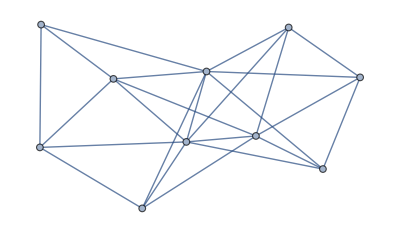
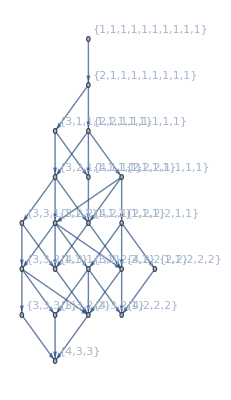

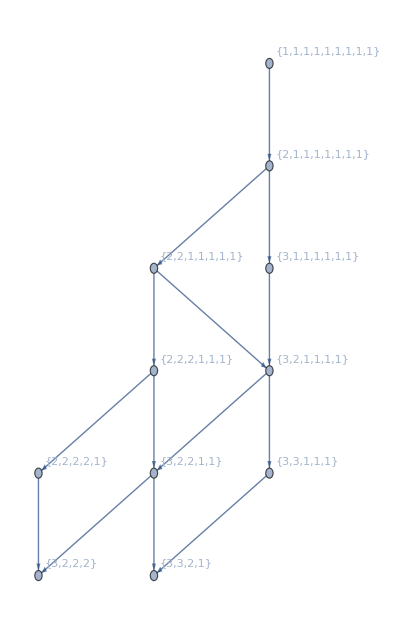
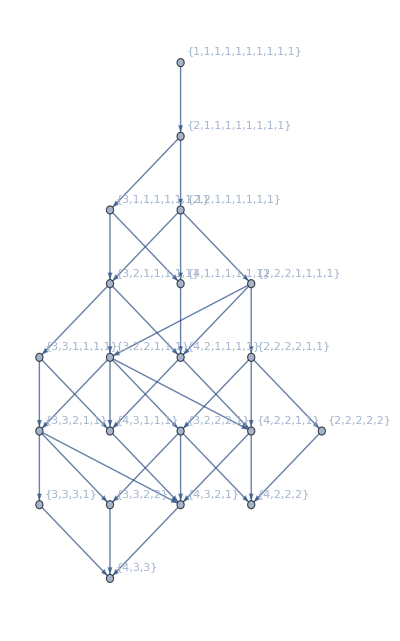
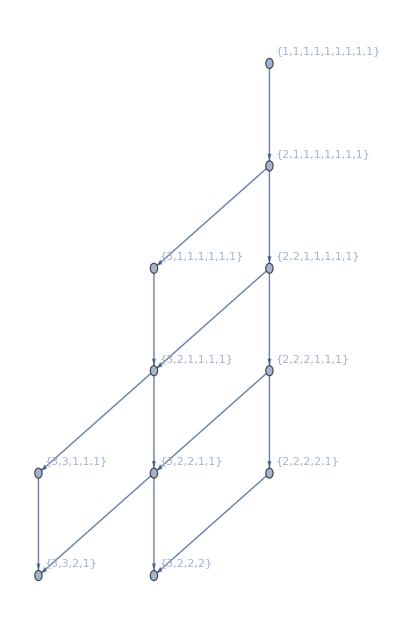
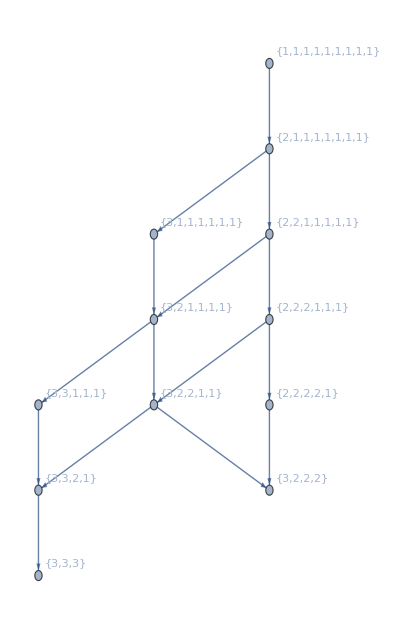
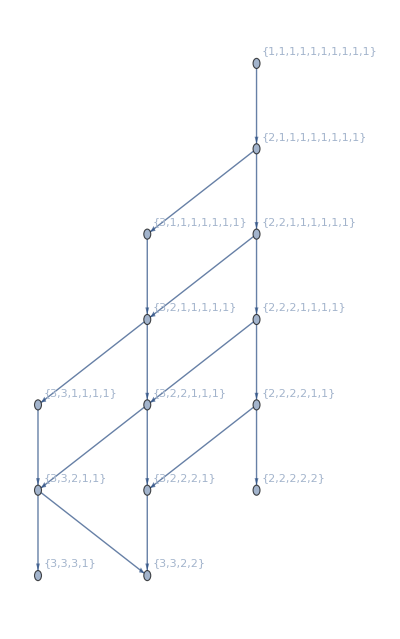
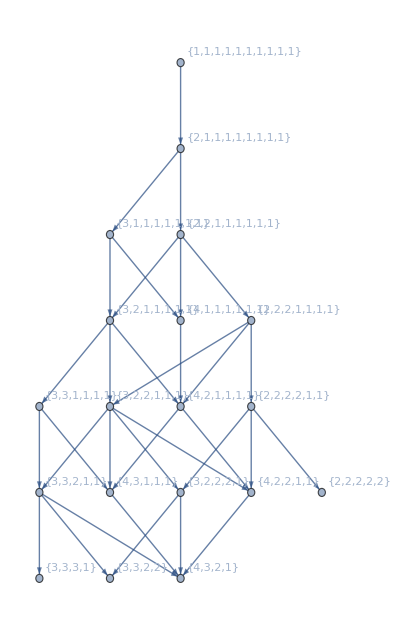
1<->2<->-Graphics--Graphics-
1<->6<->-Graphics--Graphics-
1<->7<->-Graphics--Graphics-
1<->8<->-Graphics--Graphics-
1<->10<->-Graphics--Graphics-
2<->3<->-Graphics--Graphics-
2<->4<->-Graphics--Graphics-
2<->6<->-Graphics--Graphics-
2<->8<->-Graphics--Graphics-
3<->5<->-Graphics--Graphics-
3<->7<->-Graphics--Graphics-
3<->9<->-Graphics--Graphics-
3<->10<->-Graphics--Graphics-
4<->6<->-Graphics--Graphics-
5<->9<->-Graphics--Graphics-
6<->7<->-Graphics--Graphics-
6<->9<->-Graphics--Graphics-
6<->10<->-Graphics--Graphics-
7<->8<->-Graphics--Graphics-
7<->10<->-Graphics--Graphics-
8<->10<->-Graphics--Graphics-

```mathematica
With[{g=With[{n=10},RandomGraph[{n,3n-6}]]},
Print[Labeled[g,Graph[PartitionTypeLattice[PartitionTypes[g]],VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]]];
DoItFroGraph2[g]//TableForm
]
```